# Recurrence Equations for ∫cos^m(z)(A+B cos(z)+C cos^2(z))(a+b cos(z))^n ⅆz when a^2≠b^2

#### Recurrence T2.4a:

(m+1)∫Cos[z]^m(A+B Cos[z]+C Cos[z]^2) (a+b Cos[z])^n ⅆz=
-A Sin[z]Cos[z]^(m+1)(a+b Cos[z])^n+
∫Cos[z]^(m+1)(a B(m+1)-b A n+((a C+b B) (m+1)+a A (m+2)) Cos[z]+
b(C(m+1)+A (m+n+2))Cos[z]^2)(a+b Cos[z])^(n-1)ⅆz

#### Recurrence T2.4b:

b(n+1)(a^2-b^2)∫Cos[z]^m(A+B Cos[z]+C Cos[z]^2) (a+b Cos[z])^n ⅆz =
(a^2 C-a b B+b^2 A) Sin[z]Cos[z]^m(a+b Cos[z])^(n+1)+
∫Cos[z]^(m-1)(m (a^2 C-a b B+b^2 A)+b(n+1)(a (C+A)-b B)Cos[z]-
(a^2 C(m+1)-a b B (m+n+2)+b^2 (A (m+n+2)+C (n+1)))Cos[z]^2)(a+b Cos[z])^(n+1)ⅆz

#### Recurrence T2.5a:

a(m+1)∫Cos[z]^m(A+B Cos[z]+C Cos[z]^2) (a+b Cos[z])^n ⅆz=
-A Sin[z]Cos[z]^(m+1)(a+b Cos[z])^(n+1)+
∫Cos[z]^(m+1) (a B(m+1)-b A (m+n+2)+a(A(m+2)+C(m+1))Cos[z]+
b A(m+n+3)Cos[z]^2 )(a+b Cos[z])^n ⅆz

#### Recurrence T2.5b:

b(m+n+2)∫Cos[z]^m(A+B Cos[z]+C Cos[z]^2) (a+b Cos[z])^n ⅆz=
C Sin[z]Cos[z]^m(a+b Cos[z])^(n+1)+
∫Cos[z]^(m-1) (a C m+(b A(m+n+2)+b C(m+n+1))Cos[z]+
(b B(m+n+2)-a C(m+1))Cos[z]^2)(a+b Cos[z])^n ⅆz

#### Recurrence T2.6a:

a(n+1) (a^2-b^2)∫Cos[z]^m(A+B Cos[z]+C Cos[z]^2) (a+b Cos[z])^n ⅆz=
-(b^2 A-a b B+a^2 C) Sin[z]Cos[z]^(m+1)(a+b Cos[z])^(n+1)+
 ∫Cos[z]^m (A (a^2 (n+1)-b^2 (m+n+2))-a (a C-b B) (m+1)-a(n+1)(b A-a B+b C)Cos[z]+
(m+n+3) (b^2 A-a b B+a^2 C)Cos[z]^2)(a+b Cos[z])^(n+1)ⅆz

#### Recurrence T2.6b:

(m+n+2)∫Cos[z]^m(A+B Cos[z]+C Cos[z]^2) (a+b Cos[z])^n ⅆz=
C Sin[z]Cos[z]^(m+1)(a+b Cos[z])^n+
 ∫Cos[z]^m (a (A(m+n+2)+C (m+1))+((b A+a B)(m+n+2)+b C(m+n+1))Cos[z]+
(b B (m+n+2)+a C n)Cos[z]^2)(a+b Cos[z])^(n-1)ⅆz

# Integration Rules for ∫cos^m(z)(a+b cos(z))^n ⅆz when a^2≠b^2

## Domain Map of Rules

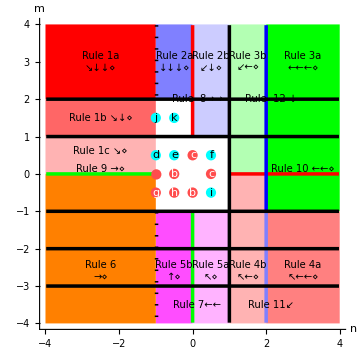

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

## Rules for Specific Points

Rule a:    ∫1/(a+b Cos[c+d x])ⅆx

#### Note: Although this rule is slightly more complicated than the following rule, it produces continuous antiderivatives when a^2-b^2>0.

#### Rule a1: If a^2-b^2>0, then

∫1/(a+b Cos[c+d x])ⅆx  ⟶  x/(√(a^2-b^2))-2/(d √(a^2-b^2))ArcTan[(b Sin[c+d x])/(a+√(a^2-b^2)+b Cos[c+d x])]

#### Program code:

```mathematica
Int[1/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  x/Rt[a^2-b^2,2] - 2/(d*Rt[a^2-b^2,2])*ArcTan[Sim[b*Sin[c+d*x]/(a+Rt[a^2-b^2,2]+b*Cos[c + d*x])]] /;
FreeQ[{a,b,c,d},x] && PositiveQ[a^2-b^2]
```

#### Reference: G&R 2.553.3a, A&S 4.3.133a

#### Rule a2: If a^2-b^2>0, then

∫1/(a+b Cos[c+d x])ⅆx  ⟶  2/(d √(a^2-b^2))ArcTan[((a-b) Tan[1/2 (c+d x)])/(√(a^2-b^2))]

#### Program code:

```mathematica
Int[1/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  2*ArcTan[(a-b)*Tan[(c+d*x)/2]/Rt[a^2-b^2,2]]/(d*Rt[a^2-b^2,2]) /;
FreeQ[{a,b,c,d},x] && PosQ[a^2-b^2]
```

#### Reference: G&R 2.553.3b', A&S 4.3.133b'

#### Rule a3: If ¬(a^2-b^2>0), then

∫1/(a+b Cos[c+d x])ⅆx  ⟶  -2/(d √(b^2-a^2))ArcTanh[((a-b) Tan[1/2 (c+d x)])/(√(b^2-a^2))]

#### Program code:

```mathematica
Int[1/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  -2*ArcTanh[(a-b)*Tan[(c+d*x)/2]/Rt[b^2-a^2,2]]/(d*Rt[b^2-a^2,2]) /;
FreeQ[{a,b,c,d},x] && NegQ[a^2-b^2]
```

Rule b:    ∫1/(√(a+b Cos[c+d x]))ⅆx

#### Basis: ∂_x EllipticF[x,n]=1/(√(1-n Sin[x]^2))

#### Rule b1: If a^2-b^2≠0 ∧ a+b>0, then

∫1/(√(a+b Cos[c+d x]))ⅆx  ⟶  2/(d √(a+b))EllipticF[(c+d x)/2,(2 b)/(a+b)]

#### Program code:

```mathematica
Int[1/Sqrt[a_.+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  2*EllipticF[(c+d*x)/2,Sim[2*b/(a+b)]]/(d*Sqrt[a+b]) /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && PositiveQ[a+b]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_x (√((a+b f[c+d x])/(a+b)))/(√(a+b f[c+d x]))=0

#### Note: Since a/(a+b)+b/(a+b)=1>0, above rule applies to resulting integrand.

#### Rule b2: If a^2-b^2≠0 ∧ ¬(a+b>0), then

∫1/(√(a+b Cos[c+d x]))ⅆx  ⟶  (√((a+b Cos[c+d x])/(a+b)))/(√(a+b Cos[c+d x]))∫1/(√(a/(a+b)+b/(a+b)Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[1/Sqrt[a_.+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Sqrt[(a+b*Cos[c+d*x])/(a+b)]/Sqrt[a+b*Cos[c+d*x]]*Int[1/Sqrt[a/(a+b)+b/(a+b)*Cos[c+d*x]],x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && Not[PositiveQ[a+b]]
```

Rule c:    ∫√(a+b Cos[c+d x])ⅆx

#### Basis: ∂_z EllipticE[z,n]=√(1-n Sin[z]^2)

#### Basis: 1-(2 b)/(a+b)Sin[1/2 (c+d x)]^2=a/(a+b)+(b Cos[c+d x])/(a+b)

#### Rule c1: If a^2-b^2≠0 ∧ a+b>0, then

∫√(a+b Cos[c+d x])ⅆx  ⟶  (2 √(a+b))/dEllipticE[(c+d x)/2,(2 b)/(a+b)]

#### Program code:

```mathematica
Int[Sqrt[a_.+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  2*Sqrt[a+b]*EllipticE[(c+d*x)/2,Sim[2*b/(a+b)]]/d /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && PositiveQ[a+b]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_x (√(a+b f[c+d x]))/(√((a+b f[c+d x])/(a+b)))=0

#### Note: Since a/(a+b)+b/(a+b)=1>0, above rule applies to resulting integrand.

#### Rule c2: If a^2-b^2≠0 ∧ ¬(a+b>0), then

∫√(a+b Cos[c+d x])ⅆx  ⟶  (√(a+b Cos[c+d x]))/(√((a+b Cos[c+d x])/(a+b)))∫√(a/(a+b)+b/(a+b)Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Sqrt[a_.+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Sqrt[a+b*Cos[c+d*x]]/Sqrt[(a+b*Cos[c+d*x])/(a+b)]*Int[Sqrt[a/(a+b)+b/(a+b)*Cos[c+d*x]],x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && Not[PositiveQ[a+b]]
```

Rule d:    ∫(√Cos[c+d x])/(a+b Cos[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: (√z)/(a+b z)=1/(b √z)-a/(b √z (a+b z))

#### Rule d: If a^2-b^2≠0, then

∫(√Cos[c+d x])/(a+b Cos[c+d x])ⅆx  ⟶  1/b∫1/(√Cos[c+d x])ⅆx-a/b∫1/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[Cos[c_.+d_.*x_]]/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  Dist[1/b,Int[1/Sqrt[Cos[c+d*x]],x]] - 
  Dist[a/b,Int[1/(Sqrt[Cos[c+d*x]]*(a+b*Cos[c+d*x])),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule e:    ∫(√Cos[c+d x])/(√(a+b Cos[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Note: The resulting integrands appear more complicated than the original, but there exists terminal rules for both.

#### Rule e: If a^2-b^2≠0

∫(√Cos[c+d x])/(√(a+b Cos[c+d x]))ⅆx  ⟶  ∫(1+Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx-∫1/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[Cos[c_.+d_.*x_]]/Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Int[(1+Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] - 
  Int[1/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Basis: If b>0 ∧ b-a>0, then √(a+b z)=√(1+z) √((a+b z)/(1+z))

#### Rule: If b>0 ∧ b^2-a^2>0, then

∫(A+A Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx  ⟶  (4A)/(d √(a+b))EllipticPi[-1,ArcSin[Tan[(c+d x)/2]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  4*A/(d*Sqrt[a+b])*EllipticPi[-1,ArcSin[Tan[(c+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√-z)/(√z)=0

#### Rule: If b<0 ∧ b^2-a^2>0, then

∫(A-A Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx  ⟶  (√(-Cos[c+d x]))/(√Cos[c+d x])∫(A-A Cos[c+d x])/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  Sqrt[-Cos[c+d*x]]/Sqrt[Cos[c+d*x]]*Int[(A+A*Cos[c+d*x])/(Sqrt[-Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A+B] && NegativeQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1+z))/(√(a+b z))√((a+b z)/((a+b) (1+z))))=0

#### Rule: If a^2-b^2≠0, then

∫(A+A Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))  ⟶  
(4A √(1+Cos[c+d x]))/(d √(a+b Cos[c+d x]))√((a+b Cos[c+d x])/((a+b) (1+Cos[c+d x])))EllipticPi[-1,ArcSin[Tan[(c+d x)/2]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  4*A*Sqrt[1+Cos[c+d*x]]/(d*Sqrt[a+b*Cos[c+d*x]])*
  Sqrt[(a+b*Cos[c+d*x])/((a+b)*(1+Cos[c+d*x]))]*
  EllipticPi[-1,ArcSin[Tan[(c+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && NonzeroQ[a^2-b^2]
```

Rule e':    ∫(√(-Cos[c+d x]))/(√(a+b Cos[c+d x]))ⅆx

#### Derivation: Algebraic expansion

#### Note: The resulting integrands appear more complicated than the original, but there exists terminal rules for both.

#### Rule e': If a^2-b^2≠0

∫(√(-Cos[c+d x]))/(√(a+b Cos[c+d x]))ⅆx  ⟶  ∫(1-Cos[c+d x])/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))ⅆx-∫1/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[-Cos[c_.+d_.*x_]]/Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Int[(1-Cos[c+d*x])/(Sqrt[-Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] - 
  Int[1/(Sqrt[-Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Basis: If b<0 ∧ b+a<0, then √(a+b z)=√(1-z) √((a+b z)/(1-z))

#### Rule: If b<0 ∧ b^2-a^2>0, then

∫(A-A Cos[c+d x])/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))ⅆx  ⟶  -(4A)/(d √(a-b))EllipticPi[-1,ArcSin[Cot[(c+d x)/2]],-(a+b)/(a-b)]

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[-Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  -4*A/(d*Sqrt[a-b])*EllipticPi[-1,ArcSin[Cot[(c+d*x)/2]],-Sim[(a+b)/(a-b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A+B] && NegativeQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z (√z)/(√-z)=0

#### Rule: If b>0 ∧ b^2-a^2>0, then

∫(A+A Cos[c+d x])/(√(-Cos[c+d x])√(a+b Cos[c+d x]))ⅆx  ⟶  (√Cos[c+d x])/(√(-Cos[c+d x]))∫(A+A Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[-Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  Sqrt[Cos[c+d*x]]/Sqrt[-Cos[c+d*x]]*Int[1/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1-z))/(√(a+b z))√((a+b z)/((a-b) (1-z))))=0

#### Rule: If a^2-b^2≠0, then

∫(A-A Cos[c+d x])/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))  ⟶  
-(4A √(1-Cos[c+d x]))/(d √(a+b Cos[c+d x]))√((a+b Cos[c+d x])/((a-b) (1-Cos[c+d x])))EllipticPi[-1,ArcSin[Cot[(c+d x)/2]],-(a+b)/(a-b)]

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[-Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  -4*A*Sqrt[1-Cos[c+d*x]]/(d*Sqrt[a+b*Cos[c+d*x]])*
  Sqrt[(a+b*Cos[c+d*x])/((a-b)*(1-Cos[c+d*x]))]*
  EllipticPi[-1,ArcSin[Cot[(c+d*x)/2]],-Sim[(a+b)/(a-b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A+B] && NonzeroQ[a^2-b^2]
```

Rule f:    ∫√Cos[c+d x] √(a+b Cos[c+d x])ⅆx

#### Rule f: If a^2-b^2≠0, then

∫√Cos[c+d x] √(a+b Cos[c+d x])ⅆx  ⟶  (√Cos[c+d x] √(a+b Cos[c+d x]) Tan[1/2 (c+d x)])/d+
∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (1+Cos[c+d x]))ⅆx-a/2∫(1-Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]*Tan[(1/2)*(c+d*x)]/d + 
  Int[Sqrt[a+b*Cos[c+d*x]]/(Sqrt[Cos[c+d*x]]*(1+Cos[c+d*x])),x] - 
  Dist[a/2,Int[(1-Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule g:    ∫1/(√Cos[c+dx](a+b Cos[c+dx]))ⅆx

#### Basis: ∂_z EllipticPi[n,z/2,2]=1/(√Cos[z] (2-n+n Cos[z]))

#### Rule g: If a^2-b^2≠0, then

∫1/(√Cos[c+dx](a+b Cos[c+dx]))ⅆx  ⟶  2/(d(a+b))EllipticPi[(2 b)/(a+b),(c+d x)/2,2]

#### Program code:

```mathematica
Int[1/(Sqrt[Cos[c_.+d_.*x_]]*(a_+b_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  2/(d*(a+b))*EllipticPi[Sim[2*b/(a+b)],(c+d*x)/2,2] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule h:    ∫1/(√Cos[c+dx]√(a+b Cos[c+dx]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: If b>0 ∧ b-a>0, then √(a+b z)=√(1+z) √((a+b z)/(1+z))

#### Rule h1: If b>0 ∧ b^2-a^2>0, then

∫1/(√Cos[c+d x]√(a+b Cos[c+d x]))ⅆx  ⟶  2/(d √(a+b))EllipticF[ArcSin[Tan[(c+d x)/2]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[1/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_.+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  2/(d*Sqrt[a+b])*EllipticF[ArcSin[Tan[(c+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d},x] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Rule h2: If b<0 ∧ b^2-a^2>0, then

∫1/(√Cos[c+d x]√(a+b Cos[c+d x]))ⅆx  ⟶  (√(-Cos[c+d x]))/(√Cos[c+d x])∫1/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[1/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  Sqrt[-Cos[c+d*x]]/Sqrt[Cos[c+d*x]]*Int[1/(Sqrt[-Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && NegativeQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1+z))/(√(a+b z))√((a+b z)/((a+b) (1+z))))=0

#### Rule h3: If a^2-b^2≠0, then

∫1/(√Cos[c+d x] √(a+b Cos[c+d x]))  ⟶  
(2 √(1+Cos[c+d x]))/(d √(a+b Cos[c+d x]))√((a+b Cos[c+d x])/((a+b) (1+Cos[c+d x])))EllipticF[ArcSin[Tan[(c+d x)/2]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[1/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_.+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  2*Sqrt[1+Cos[c+d*x]]/(d*Sqrt[a+b*Cos[c+d*x]])*
  Sqrt[(a+b*Cos[c+d*x])/((a+b)*(1+Cos[c+d*x]))]*
  EllipticF[ArcSin[Tan[(c+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule h':    ∫1/(√(-Cos[c+dx])√(a+b Cos[c+dx]))ⅆx

#### Derivation: Algebraic expansion

#### Basis: If b<0 ∧ b+a<0, then √(a+b z)=√(1-z) √((a+b z)/(1-z))

#### Rule h1': If b<0 ∧ b^2-a^2>0, then

∫1/(√(-Cos[c+d x])√(a+b Cos[c+d x]))ⅆx  ⟶  -2/(d √(a-b))EllipticF[ArcSin[Cot[(c+d x)/2]],-(a+b)/(a-b)]

#### Program code:

```mathematica
Int[1/(Sqrt[-Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  -2/(d*Sqrt[a-b])*EllipticF[ArcSin[Cot[(c+d*x)/2]],-Sim[(a+b)/(a-b)]] /;
FreeQ[{a,b,c,d},x] && NegativeQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Rule h2': If b>0 ∧ b^2-a^2>0, then

∫1/(√(-Cos[c+d x])√(a+b Cos[c+d x]))ⅆx  ⟶  (√Cos[c+d x])/(√(-Cos[c+d x]))∫1/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[1/(Sqrt[-Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  Sqrt[Cos[c+d*x]]/Sqrt[-Cos[c+d*x]]*Int[1/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d},x] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(1-z))/(√(a+b z))√((a+b z)/((a-b) (1-z))))=0

#### Rule h3': If a^2-b^2≠0, then

∫1/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))  ⟶  
-(2 √(1-Cos[c+d x]))/(d √(a+b Cos[c+d x]))√((a+b Cos[c+d x])/((a-b) (1-Cos[c+d x])))EllipticF[ArcSin[Cot[(c+d x)/2]],-(a+b)/(a-b)]

#### Program code:

```mathematica
Int[1/(Sqrt[-Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  -2*Sqrt[1-Cos[c+d*x]]/(d*Sqrt[a+b*Cos[c+d*x]])*
  Sqrt[(a+b*Cos[c+d*x])/((a-b)*(1-Cos[c+d*x]))]*
  EllipticF[ArcSin[Cot[(c+d*x)/2]],-Sim[(a+b)/(a-b)]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule i:    ∫(√(a+b Cos[c+d x]))/(√Cos[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Note: The resulting integrands appear more complicated than the original, but there exists terminal rules for both.

#### Rule i: If a^2-b^2≠0

∫(√(a+b Cos[c+d x]))/(√Cos[c+d x])ⅆx  ⟶  (a-b)∫1/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx+b∫(1+Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*Cos[c_.+d_.*x_]]/Sqrt[Cos[c_.+d_.*x_]],x_Symbol] :=
  Dist[a-b,Int[1/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x]] + 
  Dist[b,Int[(1+Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

#### Derivation: Algebraic expansion

#### Basis: If b>0 ∧ b-a>0, then √(a+b z)=√(1+z) √((a+b z)/(1+z))

#### Rule: If b>0 ∧ b^2-a^2>0, then

∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (A+A Cos[c+d x]))ⅆx  ⟶  (√(a+b))/(d A)EllipticE[ArcSin[Tan[(c+d x)/2]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*Cos[c_.+d_.*x_]]/(Sqrt[Cos[c_.+d_.*x_]]*(A_+B_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  Sqrt[a+b]/(d*A)*EllipticE[ArcSin[Tan[(c+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && PositiveQ[b] && PositiveQ[b^2-a^2]
```

#### Derivation: Piecewise constant extraction

#### Rule: If b<0 ∧ b^2-a^2>0, then

∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (A-A Cos[c+d x]))ⅆx  ⟶  (√(-Cos[c+d x]))/(√Cos[c+d x])∫(A-A Cos[c+d x])/(√(-Cos[c+d x]) √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
(* Int[Sqrt[a_+b_.*Cos[c_.+d_.*x_]]/(Sqrt[Cos[c_.+d_.*x_]]*(A_+B_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  Sqrt[-Cos[c+d*x]]/Sqrt[Cos[c+d*x]]*Int[(A+A*Cos[c+d*x])/(Sqrt[-Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A+B] && NegativeQ[b] && PositiveQ[b^2-a^2] *)
```

#### Derivation: Piecewise constant extraction

#### Basis: ∂_z ((√(a+b z))/(√(1+z))/√((a+b z)/((a+b) (1+z))))=0

#### Rule: If a^2-b^2≠0, then

∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (A+A Cos[c+d x]))  ⟶  
(√(a+b Cos[c+d x]))/(d A √(1+ Cos[c+d x])√((a+b Cos[c+d x])/((a+b) (1+Cos[c+d x]))))EllipticE[ArcSin[Tan[(c+d x)/2]],-(a-b)/(a+b)]

#### Program code:

```mathematica
Int[Sqrt[a_+b_.*Cos[c_.+d_.*x_]]/(Sqrt[Cos[c_.+d_.*x_]]*(A_+B_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  Sqrt[a+b*Cos[c+d*x]]/(d*A*Sqrt[1+Cos[c+d*x]]*Sqrt[(a+b*Cos[c+d*x])/((a+b)*(1+Cos[c+d*x]))])*
  EllipticE[ArcSin[Tan[(c+d*x)/2]],-Sim[(a-b)/(a+b)]] /;
FreeQ[{a,b,c,d,A,B},x] && ZeroQ[A-B] && NonzeroQ[a^2-b^2]
```

Rule j:    ∫Cos[c+d x]^(3/2)/(a+b Cos[c+d x])ⅆx

#### Derivation: Algebraic expansion

#### Basis: z^(3/2)/(a+b z)=(√z)/b-(a √z)/(b (a+b z))

#### Rule j: If a^2-b^2≠0, then

∫Cos[c+d x]^(3/2)/(a+b Cos[c+d x])ⅆx  ⟶  1/b∫√Cos[c+d x]ⅆx-a/b∫(√Cos[c+d x])/(a+b Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^(3/2)/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  Dist[1/b,Int[Sqrt[Cos[c+d*x]],x]] - 
  Dist[a/b,Int[Sqrt[Cos[c+d*x]]/(a+b*Cos[c+d*x]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

Rule k:    ∫Cos[c+d x]^(3/2)/(√(a+b Cos[c+d x]))ⅆx

#### Rule k: If a^2-b^2≠0, then

∫Cos[c+d x]^(3/2)/(√(a+b Cos[c+d x]))ⅆx  ⟶  (√Cos[c+d x] √(a+b Cos[c+d x]) Tan[(c+d x)/2])/(b d)+
1/b∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (1+Cos[c+d x]))ⅆx-a/(2 b)∫(1+Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^(3/2)/Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]*Tan[(c+d*x)/2]/(b*d) + 
  Dist[1/b,Int[Sqrt[a+b*Cos[c+d*x]]/(Sqrt[Cos[c+d*x]]*(1+Cos[c+d*x])),x]] - 
  Dist[a/(2*b),Int[(1+Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2]
```

## Rules 7-8: ∫Cos[c+d x]^m ⅆx

#### Reference: G&R 2.01.6, CRC 291, A&S 4.3.114

#### Derivation: Primitive rule

#### Basis: Sin'[z]=Cos[z]

#### Rule 8a:

∫Cos[a+b x]ⅆx  ⟶  Sin[a+b x]/b

#### Program code:

```mathematica
Int[Cos[a_.+b_.*x_],x_Symbol] :=
  Sin[a+b*x]/b /;
FreeQ[{a,b},x]
```

#### Derivation: Integration by substitution

#### Basis: If (n-1)/2∈ℤ, then Cos[z]^n=(1-Sin[z]^2)^((n-1)/2) Sin'[z]

#### Note: This rule is used for odd n>1 since it requires fewer steps and results in a simpler antiderivative than the following rule.

#### Rule 8b: If n>1 ∧ (n-1)/2∈ℤ, then

∫Cos[a+b x]^n ⅆx  ⟶  1/bSubst[∫(1-x^2)^((n-1)/2)ⅆx,x,Sin[a+b x]]

#### Program code:

```mathematica
Int[Cos[a_.+b_.*x_]^n_,x_Symbol] :=
  Dist[1/b,ReplaceAll[Int[Expand[(1-x^2)^((n-1)/2),x],x],x->Sin[a+b*x]]] /;
FreeQ[{a,b},x] && OddQ[n] && n>1
```

#### Reference: G&R 2.554.3 inverted special case when a=0

#### Derivation: Recurrence T2.6b with A=0, B=0, C=b, m=-1, n=n-1 and a=0

#### Rule 8c: If n>1 ∧ (n-1)/2∉ℤ, then

∫(b Cos[c+d x])^n ⅆx  ⟶  (b Sin[c+d x] (b Cos[c+d x])^(n-1))/(d n)+((n-1) b^2)/n∫(b Cos[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[(b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b*Sin[c+d*x]*(b*Cos[c+d*x])^(n-1)/(d*n) +
  Dist[(n-1)*b^2/n,Int[(b*Cos[c+d*x])^(n-2),x]] /;
FreeQ[{b,c,d},x] && RationalQ[n] && n>1 && Not[OddQ[n]]
```

#### Reference: G&R 2.554.3 special case when a=0

#### Derivation: Recurrence T2.6a with A=0, B=1, C=0, m=-1 and a=0

#### Rule 7: If n∈𝔽 ∧ n<-1, then

∫(b Cos[c+d x])^n ⅆx  ⟶  -(Sin[c+d x] (b Cos[c+d x])^(n+1))/(b d (n+1))+(n+2)/((n+1) b^2)∫(b Cos[c+d x])^(n+2)ⅆx

#### Program code:

```mathematica
Int[(b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -Sin[c+d*x]*(b*Cos[c+d*x])^(n+1)/(b*d*(n+1)) +
  Dist[(n+2)/((n+1)*b^2),Int[(b*Cos[c+d*x])^(n+2),x]] /;
FreeQ[{b,c,d},x] && RationalQ[n] && n<-1
```

## Rules 9-10: ∫(a+b Cos[c+d x])^n ⅆx

#### Reference: G&R 2.554.3

#### Derivation: Recurrence T2.6a with A=0, B=1, C=0 and m=-1

#### Rule 9: If a^2-b^2≠0 ∧ n<-1, then

∫(a+b Cos[c+d x])^n ⅆx  ⟶  (b Sin[c+d x] (a+b Cos[c+d x])^(n+1))/(d (n+1) (a^2-b^2))+                                           
                         1/((n+1) (a^2-b^2))∫(a (n+1)-b (n+2) Cos[c+d x]) (a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) +
  Dist[1/((n+1)*(a^2-b^2)),Int[(a*(n+1)-b*(n+2)*Cos[c+d*x])*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence T2.2b with m=0 and n=1

#### Note: This is rule is used whether or not a^2=b^2.

#### Rule 10a:

∫(a+b Cos[c+d x])^2 ⅆx  ⟶  ((2 a^2+b^2)x)/2+(2a b Sin[c+d x])/d+(b^2 Cos[c+d x] Sin[c+d x])/(2 d)

#### Program code:

```mathematica
Int[(a_+b_.*Cos[c_.+d_.*x_])^2,x_Symbol] :=
  (2*a^2+b^2)*x/2 + 2*a*b*Sin[c+d*x]/d + b^2*Cos[c+d*x]*Sin[c+d*x]/(2*d) /;
FreeQ[{a,b,c,d},x]
```

#### Reference: G&R 2.554.3 inverted

#### Derivation: Recurrence T2.6b with A=0, B=a, C=b, m=-1 and n=n-1

#### Rule 10b: If a^2-b^2≠0 ∧ n≥3/2 ∧ n≠2, then

∫(a+b Cos[c+d x])^n ⅆx  ⟶  (b Sin[c+d x] (a+b Cos[c+d x])^(n-1))/(d n)+                                                        
                          1/n∫(a^2 n+b^2 (n-1)+a b(2 n-1)Cos[c+d x])(a+b Cos[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n-1)/(d*n) + 
  Dist[1/n,Int[Sim[a^2*n+b^2*(n-1)+a*b*(2*n-1)*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[n] && n≥3/2 && n≠2
```

## Rules 11-12: ∫Cos[c+d x]^m(a+b Cos[c+d x])^2 ⅆx

#### Derivation: Recurrence T2.4a with A=a^2, B=2a b, C=b^2 and n=0

#### Rule 11: If a^2-b^2≠0 ∧ m<-1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^2 ⅆx  ⟶  -(a^2 Sin[c+d x]Cos[c+d x]^(m+1))/(d (m+1))+
1/(m+1)∫Cos[c+d x]^(m+1)(2 a b (m+1)+(a^2 (m+2)+b^2 (m+1)) Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_+b_.*Cos[c_.+d_.*x_])^2,x_Symbol] :=
  -a^2*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+1)) + 
  Dist[1/(m+1),Int[Cos[c+d*x]^(m+1)*(2*a*b*(m+1)+(a^2*(m+2)+b^2*(m+1))*Cos[c+d*x]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[m] && m<-1
```

#### Derivation: Recurrence T2.6b with A=a^2, B=2a b, C=b^2 and n=0

#### Rule 12: If a^2-b^2≠0 ∧ m≥-1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^2 ⅆx  ⟶  (b^2 Sin[c+d x]Cos[c+d x]^(m+1))/(d(m+2))+
1/(m+2)∫Cos[c+d x]^m (a^2(m+2)+b^2(m+1)+2a b(m+2)Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(a_+b_.*Cos[c_.+d_.*x_])^2,x_Symbol] :=
  b^2*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+2)) + 
  Dist[1/(m+2),Int[Cos[c+d*x]^m*(a^2*(m+2)+b^2*(m+1)+2*a*b*(m+2)*Cos[c+d*x]),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[m] && m≥-1
```

## Rules 1-6: ∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx

#### Derivation: Recurrence T2.4b with A=0, B=0, C=1 and m=m-2

#### Rule 1a: If a^2-b^2≠0 ∧ m>2 ∧ n<-1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
(a^2 Sin[c+d x]Cos[c+d x]^(m-2) (a+b Cos[c+d x])^(n+1))/(b d (n+1) (a^2-b^2))+1/(b(n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-3)(a^2(m-2)+a b(n+1)Cos[c+d x]-(a^2(m-1)+b^2 (n+1))Cos[c+d x]^2) (a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  a^2*Sin[c+d*x]*Cos[c+d*x]^(m-2)*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-3)*
      Sim[a^2*(m-2)+a*b*(n+1)*Cos[c+d*x]-(a^2*(m-1)+b^2*(n+1))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>2 && n<-1
```

#### Derivation: Recurrence T2.4b with A=0, B=1, C=0 and m=m-1

#### Derivation: Recurrence T2.6a with A=0, B=0, C=1 and m=m-2

#### Rule 1b: If a^2-b^2≠0 ∧ 1<m<2 ∧ n<-1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx =
-(a Sin[c+d x] Cos[c+d x]^(m-1) (a+b Cos[c+d x])^(n+1))/(d (n+1) (a^2-b^2))+1/((n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-2)(-a (m-1)-b(n+1)Cos[c+d x]+a(m+n+1)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -a*Sin[c+d*x]*Cos[c+d*x]^(m-1)*(a+b*Cos[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-2)*
      Sim[-a*(m-1)-b*(n+1)*Cos[c+d*x]+a*(m+n+1)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && 1<m<2 && n<-1
```

#### Derivation: Recurrence T2.4b with A=1, B=0 and C=0

#### Derivation: Recurrence T2.6a with A=0, B=1, C=0 and m=m-1

#### Rule 1c: If a^2-b^2≠0 ∧ 0<m<1 ∧ n<-1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx =
(b Sin[c+d x] Cos[c+d x]^m (a+b Cos[c+d x])^(n+1))/(d (n+1) (a^2-b^2))+1/((n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-1)(b m+a(n+1)Cos[c+d x]-b(m+n+2)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-1)*
      Sim[b*m+a*(n+1)*Cos[c+d*x]-b*(m+n+2)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && 0<m<1 && n<-1
```

#### Derivation: Recurrence T2.5b with A=0, B=0, C=1 and m=m-2

#### Rule 2a: If a^2-b^2≠0 ∧ m>2 ∧ -1≤n<0, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
(Sin[c+d x]Cos[c+d x]^(m-2)(a+b Cos[c+d x])^(n+1))/(b d (m+n))+1/(b (m+n))·
∫Cos[c+d x]^(m-3) (a (m-2)+b(m+n-1)Cos[c+d x]-a (m-1)Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  Sin[c+d*x]*Cos[c+d*x]^(m-2)*(a+b*Cos[c+d*x])^(n+1)/(b*d*(m+n)) + 
  Dist[1/(b*(m+n)),
    Int[Cos[c+d*x]^(m-3)*
      Sim[a*(m-2)+b*(m+n-1)*Cos[c+d*x]-a*(m-1)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>2 && -1≤n<0
```

#### Derivation: Recurrence T2.5b with A=0, B=a, C=b, m=m-1 and n=n-1

#### Derivation: Recurrence T2.6b with A=0, B=0, C=1 and m=m-2

#### Rule 2b: If a^2-b^2≠0 ∧ m>1 ∧ m≠2 ∧ 0<n<1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
(Sin[c+d x]Cos[c+d x]^(m-1)(a+b Cos[c+d x])^n)/(d (m+n))+1/(m+n)·
∫Cos[c+d x]^(m-2)(a (m-1)+b(m+n-1)Cos[c+d x]+a n Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  Sin[c+d*x]*Cos[c+d*x]^(m-1)*(a+b*Cos[c+d*x])^n/(d*(m+n)) + 
  Dist[1/(m+n),
    Int[Cos[c+d*x]^(m-2)*
      Sim[a*(m-1)+b*(m+n-1)*Cos[c+d*x]+a*n*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>1 && m≠2 && 0<n<1
```

#### Derivation: Recurrence T2.6b with A=a^2, B=2a b, C=b^2 and n=n-2

#### Rule 3a: If a^2-b^2≠0 ∧ m>-1 ∧ m≠1 ∧ m≠2 ∧ n>2, then

∫Cos[c+d x]^m (a+b Cos[c+d x])^n ⅆx  ⟶  
(b^2 Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n-2))/(d (m+n))+1/(m+n)·
 ∫Cos[c+d x]^m(a (b^2 (m+1)+a^2(m+n))+b(3 a^2 (m+n)+b^2 (m+n-1)) Cos[c+d x]+a b^2 (2m+3 n-2) Cos[c+d x]^2)(a+b Cos[c+d x])^(n-3)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b^2*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n-2)/(d*(m+n)) + 
  Dist[1/(m+n),
    Int[Cos[c+d*x]^m*
      Sim[a*(b^2*(m+1)+a^2*(m+n))+b*(3*a^2*(m+n)+b^2*(m+n-1))*Cos[c+d*x]+
        a*b^2*(2*m+3*n-2)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-3),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>-1 && m≠2 && n>2
```

#### Derivation: Recurrence T2.6b with A=0, B=a, C=b, m=m-1 and n=n-1

#### Rule 3b: If a^2-b^2≠0 ∧ m>0 ∧ m≠1 ∧ m≠2 ∧ 1<n<2, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
(b Sin[c+d x]Cos[c+d x]^m(a+b Cos[c+d x])^(n-1))/(d (m+n))+1/(m+n)·
∫Cos[c+d x]^(m-1) (a b m+(a^2(m+n)+b^2(m+n-1))Cos[c+d x]+a b (m+2 n-1)Cos[c+d x]^2)(a+b Cos[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n-1)/(d*(m+n)) + 
  Dist[1/(m+n),
    Int[Cos[c+d*x]^(m-1)*
      Sim[a*b*m+(a^2*(m+n)+b^2*(m+n-1))*Cos[c+d*x]+(a*b*(m+n)+a*b*(n-1))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>0 && m≠2 && 1<n<2
```

#### Derivation: Recurrence T2.4a with A=a^2, B=2a b, C=b^2 and n=n-2

#### Rule 4a: If a^2-b^2≠0 ∧ m<-1 ∧ n>2, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
-(a^2 Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^(n-2))/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(a^2 b (2 m-n+4)+a(3 b^2(m+1)+a^2(m+2)) Cos[c+d x]+b (b^2 (m+1)+a^2 (m+n)) Cos[c+d x]^2)(a+b Cos[c+d x])^(n-3)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -a^2*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n-2)/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      (a^2*b*(2*m-n+4)+a*(3*b^2*(m+1)+a^2*(m+2))*Cos[c+d*x]+b*(b^2*(m+1)+a^2*(m+n))*Cos[c+d*x]^2)*
      (a+b*Cos[c+d*x])^(n-3),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && n>2
```

#### Derivation: Recurrence T2.4a with A=a, B=b, C=0 and n=n-1

#### Rule 4b: If a^2-b^2≠0 ∧ m<0 ∧ m≠-1 ∧ 1<n<2, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
-(a Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^(n-1))/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(a b (m-n+2)+(b^2(m+1)+a^2 (m+2)) Cos[c+d x]+a b(m+n+1)Cos[c+d x]^2)(a+b Cos[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -a*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n-1)/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      Sim[a*b*(m-n+2)+(b^2*(m+1)+a^2*(m+2))*Cos[c+d*x]+a*b*(m+n+1)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-2),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<0 && m≠-1 && 1<n<2
```

#### Derivation: Recurrence T2.4a with A=1, B=0 and C=0

#### Derivation: Recurrence T2.5a with A=a, B=b, C=0 and n=n-1

#### Rule 5a: If a^2-b^2≠0 ∧ m<-1 ∧ 0<n<1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
-(Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^n)/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(-b n+a(m+2) Cos[c+d x]+b(m+n+2)Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_.+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^n/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      Sim[-b*n+a*(m+2)*Cos[c+d*x]+b*(m+n+2)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && 0<n<1
```

#### Derivation: Recurrence T2.5a with A=1, B=0 and C=0

#### Rule 5b: If a^2-b^2≠0 ∧ m<-1 ∧ -1≤n<0, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
-(Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d(m+1))+1/(a (m+1))·
∫Cos[c+d x]^(m+1) (-b (m+n+2)+a(m+2)Cos[c+d x]+b(m+n+3)Cos[c+d x]^2 )(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(m+1)) + 
  Dist[1/(a*(m+1)),
    Int[Cos[c+d*x]^(m+1)*
      Sim[-b*(m+n+2)+a*(m+2)*Cos[c+d*x]+b*(m+n+3)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && -1≤n<0
```

#### Derivation: Recurrence T2.6a with A=1, B=0 and C=0

#### Rule 6: If a^2-b^2≠0 ∧ m<0 ∧ n<-1, then

∫Cos[c+d x]^m(a+b Cos[c+d x])^n ⅆx  ⟶  
-(b^2 Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
 ∫Cos[c+d x]^m (a^2 (n+1)-b^2 (m+n+2)-a b(n+1)Cos[c+d x]+b^2(m+n+3)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -b^2*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^m*
      Sim[a^2*(n+1)-b^2*(m+n+2)-a*b*(n+1)*Cos[c+d*x]+(m+n+3)*(b^2)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<0 && n<-1
```

# Integration Rules for ∫cos^m(z)(A+B cos(z))(a+b cos(z))^n ⅆz when a^2≠b^2

## Domain Map of Rules

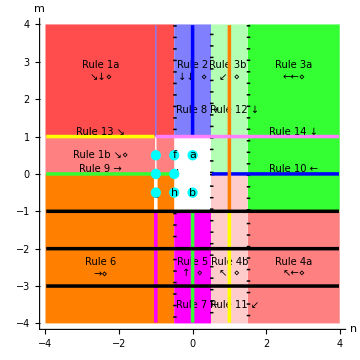

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

## Rules for Specific Points

#### Derivation: Algebraic expansion

#### Rule a:

∫√Cos[c+d x](A+B Cos[c+d x])ⅆx  ⟶  A∫√Cos[c+d x]ⅆx+B∫Cos[c+d x]^(3/2)ⅆx

#### Program code:

```mathematica
Int[Sqrt[Cos[c_.+d_.*x_]]*(A_+B_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  Dist[A,Int[Sqrt[Cos[c+d*x]],x]] + Dist[B,Int[Cos[c+d*x]^(3/2),x]] /;
FreeQ[{c,d,A,B},x]
```

#### Derivation: Algebraic expansion

#### Rule b:

∫(A+B Cos[c+d x])/(√Cos[c+d x])ⅆx  ⟶  A∫1/(√Cos[c+d x])ⅆx+B∫√Cos[c+d x]ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/Sqrt[Cos[c_.+d_.*x_]],x_Symbol] :=
  Dist[A,Int[1/Sqrt[Cos[c+d*x]],x]] + Dist[B,Int[Sqrt[Cos[c+d*x]],x]] /;
FreeQ[{c,d,A,B},x]
```

#### Reference: G&R 2.554.2

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(a+b z)=B/b+(b A-a B)/b 1/(a+b z)

#### Rule c: If b A-a B≠0, then

∫(A+B Cos[c+d x])/(a+b Cos[c+d x])ⅆx  ⟶  (B x)/b+(b A-a B)/b∫1/(a+b Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_])/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  B*x/b + Dist[(b*A-a*B)/b,Int[1/(a+b*Cos[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[b*A-a*B]
```

#### Derivation: Algebraic expansion

#### Basis: (A+B z)/(√(a+b z))=B/b √(a+b z)+(b A-a B)/b 1/(√(a+b z))

#### Rule d: If b A-a B≠0, then

∫(A+B Cos[c+d x])/(√(a+b Cos[c+d x]))ⅆx  ⟶  B/b∫√(a+b Cos[c+d x])ⅆx+(b A-a B)/b∫1/(√(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_])/Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Dist[B/b,Int[Sqrt[a+b*Cos[c+d*x]],x]] +
  Dist[(b*A-a*B)/b,Int[1/Sqrt[a+b*Cos[c+d*x]],x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[b*A-a*B]
```

#### Derivation: Algebraic expansion

#### Rule e: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(√Cos[c+d x](A+B Cos[c+d x]))/(a+b Cos[c+d x])ⅆx  ⟶ B/b ∫√Cos[c+d x]ⅆx+(b A-a B)/b∫(√Cos[c+d x])/(a+b Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Sqrt[Cos[c_.+d_.*x_]]*(A_+B_.*Cos[c_.+d_.*x_])/(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  Dist[B/b,Int[Sqrt[Cos[c+d*x]],x]] + 
  Dist[(b*A-a*B)/b,Int[Sqrt[Cos[c+d*x]]/(a+b*Cos[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

#### Derivation: Algebraic expansion

#### Note: Although more complicated, there exists a rule for the resulting integrand.

#### Rule f: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(√Cos[c+d x] (A+B Cos[c+d x]))/(√(a+b Cos[c+d x]))ⅆx  ⟶  ∫(A Cos[c+d x]+B Cos[c+d x]^2)/(√Cos[c+d x]√(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[Sqrt[Cos[c_.+d_.*x_]]*(A_+B_.*Cos[c_.+d_.*x_])/Sqrt[a_+b_.*Cos[c_.+d_.*x_]],x_Symbol] :=
  Int[(A*Cos[c+d*x]+B*Cos[c+d*x]^2)/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

#### Derivation: Algebraic expansion

#### Rule g: If a^2-b^2≠0 ∧ b A-a B≠0, then

∫(A+B Cos[c+d x])/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx  ⟶  B/b∫1/(√Cos[c+d x])ⅆx+(b A-a B)/b∫1/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[Cos[c_.+d_.*x_]]*(a_+b_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  B/b*Int[1/Sqrt[Cos[c+d*x]],x] + 
  (b*A-a*B)/b*Int[1/(Sqrt[Cos[c+d*x]]*(a+b*Cos[c+d*x])),x] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B]
```

#### Derivation: Algebraic expansion

#### Rule h: If a^2-b^2≠0 ∧ A-B≠0, then

∫(A+B Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx  ⟶  
B∫(1+Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx+(A-B)∫1/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  B*Int[(1+Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] + 
  (A-B)*Int[1/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[A-B]
```

## Rules 7-8: ∫Cos[c+d x]^m(A+B Cos[c+d x])ⅆx

#### Derivation: Recurrence T2.5a with a=1, b=0, C=0 and n=0

#### Rule 7: If m<-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x])ⅆx  ⟶  
-(A Sin[c+d x] Cos[c+d x]^(m+1))/(d(m+1))+1/(m+1)∫Cos[c+d x]^(m+1)(B(m+1)+A(m+2)Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+1)) + 
  Dist[1/(m+1),Int[Cos[c+d*x]^(m+1)*(B*(m+1)+A*(m+2)*Cos[c+d*x]),x]] /;
FreeQ[{c,d,A,B},x] && RationalQ[m] && m<-1
```

#### Derivation: Recurrence T2.5b with A=a A, B=b A+a B, C=b B and n=-1

#### Rule 8: If m>1, then

∫Cos[c+d x]^m(A+B Cos[c+d x])ⅆx  ⟶  
(B Sin[c+d x] Cos[c+d x]^m)/(d(m+1))+1/(m+1)∫Cos[c+d x]^(m-1)(B m+A (m+1)Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  B*Sin[c+d*x]*Cos[c+d*x]^m/(d*(m+1)) + 
  Dist[1/(m+1),Int[Cos[c+d*x]^(m-1)*(B*m+A*(m+1)*Cos[c+d*x]),x]] /;
FreeQ[{c,d,A,B},x] && RationalQ[m] && m>1
```

## Rules 9-10: ∫(A+B Cos[c+d x])(a+b Cos[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Basis: If b A-a B=0, then (A+B z) (a+b z)^n=B/b(a+b z)^(n+1)

#### Rule 9a: If b A-a B=0, then

∫(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  B/b∫(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  Dist[B/b,Int[(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,n},x] && ZeroQ[b*A-a*B]
```

#### Reference: G&R 2.554.1

#### Derivation: Recurrence T2.6a with A=0, B=A, C=B and m=-1

#### Rule 9b: If b A-a B≠0 ∧ a^2-b^2≠0 ∧ n<-1/2 ∧ n≠-1, then

∫(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  ((b A-a B) Sin[c+d x] (a+b Cos[c+d x])^(n+1))/(d (n+1) (a^2-b^2))+     
       1/((n+1) (a^2-b^2))∫((n+1) (a A-b B)-(n+2) (b A-a B) Cos[c+d x]) (a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  (b*A-a*B)*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) +
  Dist[1/((n+1)*(a^2-b^2)),
    Int[Sim[(n+1)*(a*A-b*B)-(n+2)*(b*A-a*B)*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[b*A-a*B] && NonzeroQ[a^2-b^2] && RationalQ[n] && n<-1/2 && n≠-1
```

#### Derivation: Recurrence T2.2b with m=0 and n=1

#### Note: This is rule is used whether or not a^2=b^2 and when A=0.

#### Rule 10a: If b A-a B≠0, then

∫(A+B Cos[c+d x]) (a+b Cos[c+d x])ⅆx  ⟶                                                                     
                             ((2 a A+b B)x)/2+((A b+a B) Sin[c+d x])/d+(b B Cos[c+d x] Sin[c+d x])/(2 d)

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
(*(2*a*A+b*B)*x/2+(2*b*A+2*a*B+b*B*Cos[c+d*x])*(Sin[c+d*x]/(2*d)) /; *)
  (2*a*A+b*B)*x/2+(A*b+a*B)*Sin[c+d*x]/d+b*B*Cos[c+d*x]*Sin[c+d*x]/(2*d) /;
FreeQ[{a,b,c,d,A,B},x]
```

#### Reference: G&R 2.554.1 inverted

#### Derivation: Recurrence T2.6b with A=0, B=A, C=B and m=-1

#### Rule 10b: If b A-a B≠0 ∧ a^2-b^2≠0 ∧ n≥1/2, then

∫(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  (B Sin[c+d x] (a+b Cos[c+d x])^n)/(d (n+1))+             
                      1/(n+1)∫(b B n+a A (n+1)+(a B n+b A (n+1)) Cos[c+d x]) (a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  B*Sin[c+d*x]*(a+b*Cos[c+d*x])^n/(d*(n+1)) + 
  Dist[1/(n+1),Int[Sim[b*B*n+a*A*(n+1)+(a*B*n+b*A*(n+1))*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[b*A-a*B] && NonzeroQ[a^2-b^2] && RationalQ[n] && n≥1/2
```

## Rule 11-12: ∫Cos[c+d x]^m(A+B Cos[c+d x])(a+b Cos[c+d x])ⅆx

#### Derivation: Recurrence T2.4a with A=a A, B=b A+a B, C=b B and n=0

#### Rule 11: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m<-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])ⅆx  ⟶  -(a A Sin[c+d x] Cos[c+d x]^(m+1))/(d(m+1))+
1/(m+1)∫Cos[c+d x]^(m+1)((b A+a B) (m+1)+(a A (m+2)+b B (m+1)) Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  -a*A*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+1)) + 
  Dist[1/(m+1),Int[Cos[c+d*x]^(m+1)*((b*A+a*B)*(m+1)+(a*A*(m+2)+b*B*(m+1))*Cos[c+d*x]),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[m] && m<-1
```

#### Derivation: Recurrence T2.6b with A=a A, B=b A+a B, C=b B and n=0

#### Rule 12: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m≥-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])ⅆx  ⟶  (b B Sin[c+d x] Cos[c+d x]^(m+1))/(d (m+2))+
1/(m+2)∫Cos[c+d x]^m (a A (m+2)+b B (m+1)+(b A+a B) (m+2) Cos[c+d x]) ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_]),x_Symbol] :=
  b*B*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+2)) + 
  Dist[1/(m+2),Int[Cos[c+d*x]^m*Sim[a*A*(m+2)+b*B*(m+1)+(b*A+a*B)*(m+2)*Cos[c+d*x],x],x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[m] && m≥-1
```

## Rules 13-14: ∫Cos[c+d x](A+B Cos[c+d x])(a+b Cos[c+d x])^n ⅆx

#### Derivation: Recurrence T2.4b with A=0, B=A, C=B and m=0

#### Rule 13: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ n<-1, then

∫Cos[c+d x](A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(a (b A-a B) Sin[c+d x](a+b Cos[c+d x])^(n+1))/(b d(n+1)(a^2-b^2))-1/(b(n+1) (a^2-b^2))·
∫(b (n+1)(b A-a B)+(a^2 B-a b A(n+2)+b^2 B(n+1)) Cos[c+d x]) (a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -a*(b*A-a*B)*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) - 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sim[b*(n+1)*
      (b*A-a*B)+(a^2*B-a*b*A*(n+2)+b^2*B*(n+1))*Cos[c+d*x],x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence T2.5b with A=0, B=A, C=B and m=0

#### Rule 14: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ n≥-1 ∧ n≠1, then

∫Cos[c+d x](A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
(B Sin[c+d x](a+b Cos[c+d x])^(n+1))/(b d (n+2))+1/(b (n+2))·
∫(b B (n+1)-(a B-b A(n+2)) Cos[c+d x])(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  B*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),Int[Sim[b*B*(n+1)-(a*B-b*A*(n+2))*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[n] && n≥-1
```

## Rules 1-6: ∫Cos[c+d x]^m(A+B Cos[c+d x])(a+b Cos[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Basis: If b A-a B=0, then A+B z=B/b(a+b z)

#### Rule 1c: If b A-a B=0, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  B/b∫Cos[c+d x]^m(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  Dist[B/b,Int[Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,m,n},x] && ZeroQ[b*A-a*B]
```

#### Derivation: Recurrence T2.4b with A=0, B=A, C=B and m=m-1

#### Rule 1a: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m>1 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(a(b A-a B) Sin[c+d x] Cos[c+d x]^(m-1) (a+b Cos[c+d x])^(n+1))/(b d (n+1) (a^2-b^2))-1/(b(n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-2)(a(m-1) (b A-a B)+b(n+1)(b A-a B)Cos[c+d x]+(a^2 B m-a b A (m+n+1)+b^2 B (n+1))Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -a*(b*A-a*B)*Sin[c+d*x]*Cos[c+d*x]^(m-1)*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) - 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-2)*
      Sim[a*(m-1)*(b*A-a*B)+b*(n+1)*(b*A-a*B)*Cos[c+d*x]+(a^2*B*m-a*b*A*(m+n+1)+
        b^2*B*(n+1))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m>1 && n<-1/2 && n≠-1
```

#### Derivation: Recurrence T2.4b with C=0

#### Derivation: Recurrence T2.6a with A=0, B=A, C=B and m=m-1

#### Rule 1b: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ 0<m<1 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
((b A-a B) Sin[c+d x] Cos[c+d x]^m (a+b Cos[c+d x])^(n+1))/(d (n+1) (a^2-b^2))+1/((n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-1)(m (b A-a B)+(n+1)(a A-b B)Cos[c+d x]-(b A-a B)(m+n+2)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  (b*A-a*B)*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1)/(d*(n+1)*(a^2-b^2)) + 
  Dist[1/((n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-1)*
      Sim[m*(b*A-a*B)+(n+1)*(a*A-b*B)*Cos[c+d*x]-(b*A-a*B)*(m+n+2)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  0<m<1 && n<-1/2 && n≠-1
```

#### Derivation: Recurrence T2.5b with A=0, B=A, C=B and m=m-1

#### Rule 2: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m>1 ∧ (-1/2≤n<1/2 ∨ n=-1), then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
(B Sin[c+d x]Cos[c+d x]^(m-1)(a+b Cos[c+d x])^(n+1))/(b d (m+n+1))+1/(b (m+n+1))·
∫Cos[c+d x]^(m-2) (a B (m-1)+b B(m+n)Cos[c+d x]+(b A(m+n+1)-a B m)Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  B*Sin[c+d*x]*Cos[c+d*x]^(m-1)*(a+b*Cos[c+d*x])^(n+1)/(b*d*(m+n+1)) + 
  Dist[1/(b*(m+n+1)),
    Int[Cos[c+d*x]^(m-2)*
      Sim[a*B*(m-1)+b*B*(m+n)*Cos[c+d*x]+(b*A*(m+n+1)-a*B*m)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m>1 && (-1/2≤n<1/2 || n==-1)
```

#### Derivation: Recurrence T2.6b with A=a A, B=b A+a B, C=b B and n=n-1

#### Rule 3a: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m≥-1 ∧ m≠1 ∧ n≥3/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
(b B Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n-1))/(d (m+n+1))+1/(m+n+1)·
 ∫Cos[c+d x]^m(a (b B (m+1)+a A (m+n+1))+(b^2 B (m+n)+a (2 A b+a B) (m+n+1)) Cos[c+d x]+b (A b (m+n+1)+a B (m+2 n)) Cos[c+d x]^2)(a+b Cos[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  b*B*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n-1)/(d*(m+n+1)) + 
  Dist[1/(m+n+1),
    Int[Cos[c+d*x]^m*
      Sim[a*(b*B*(m+1)+a*A*(m+n+1))+(b^2*B*(m+n)+a*(2*A*b+a*B)*(m+n+1))*Cos[c+d*x]+
        b*(A*b*(m+n+1)+a*B*(m+2*n))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-2),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m≥-1 && n≥3/2
```

#### Derivation: Recurrence T2.6b with A=0, B=A, C=B and m=m-1

#### Rule 3b: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m>0 ∧ m≠1 ∧ 1/2≤n<3/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
(B Sin[c+d x]Cos[c+d x]^m(a+b Cos[c+d x])^n)/(d (m+n+1))+1/(m+n+1)·
 ∫Cos[c+d x]^(m-1) (a B m+(a A(m+n+1)+b B(m+n))Cos[c+d x]+(b A (m+n+1)+a B n)Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  B*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^n/(d*(m+n+1)) + 
  Dist[1/(m+n+1),
    Int[Cos[c+d*x]^(m-1)*
      Sim[a*B*m+(a*A*(m+n+1)+b*B*(m+n))*Cos[c+d*x]+(b*A*(m+n+1)+a*B*n)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m>0 && 1/2≤n<3/2
```

#### Derivation: Recurrence T2.4a with A=a A, B=b A+a B, C=b B and n=n-1

#### Rule 4a: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m<-1 ∧ n≥3/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(a A Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^(n-1))/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(a ((b A+a B) (m+1)-b A (n-1))+(b (b A+2 a B) (m+1)+a^2 A (m+2)) Cos[c+d x]+b (b B (m+1)+a A (m+n+1)) Cos[c+d x]^2)(a+b Cos[c+d x])^(n-2)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -a*A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n-1)/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      Sim[a*((b*A+a*B)*(m+1)-b*A*(n-1))+(b*(b*A+2*a*B)*(m+1)+a^2*A*(m+2))*Cos[c+d*x]+
        b*(b*B*(m+1)+a*A*(m+n+1))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-2),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m<-1 && n≥3/2
```

#### Derivation: Recurrence T2.4a with C=0

#### Rule 4b: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m<0 ∧ m≠-1 ∧ 1/2≤n<3/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(A Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^n)/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(a B(m+1)-b A n+(b B(m+1)+a A (m+2)) Cos[c+d x]+b A(m+n+2)Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^n/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      Sim[a*B*(m+1)-b*A*n+(b*B*(m+1)+a*A*(m+2))*Cos[c+d*x]+b*A*(m+n+2)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m<0 && m≠-1 && 1/2≤n<3/2
```

#### Derivation: Recurrence T2.5a with C=0

#### Rule 5: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m<-1 ∧ (-1/2≤n<1/2 ∨ n=-1), then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(A Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d(m+1))+1/(a (m+1))·
∫Cos[c+d x]^(m+1) (a B(m+1)-b A (m+n+2)+a A(m+2)Cos[c+d x]+b A(m+n+3)Cos[c+d x]^2 )(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(m+1)) + 
  Dist[1/(a*(m+1)),
    Int[Cos[c+d*x]^(m+1)*
      Sim[a*B*(m+1)-b*A*(m+n+2)+a*A*(m+2)*Cos[c+d*x]+b*A*(m+n+3)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m<-1 && (-1/2≤n<1/2 || n==-1)
```

#### Derivation: Recurrence T2.6a with C=0

#### Rule 6: If a^2-b^2≠0 ∧ b A-a B≠0 ∧ m<0 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(b(b A-a B) Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
 ∫Cos[c+d x]^m (A (a^2 (n+1)-b^2 (m+n+2))+a b B(m+1)-a(n+1)(b A-a B)Cos[c+d x]+b(b A-a B)(m+n+3)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_])*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -b*(b*A-a*B)*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^m*
      Sim[A*(a^2*(n+1)-b^2*(m+n+2))+a*b*B*(m+1)-a*(n+1)*(b*A-a*B)*Cos[c+d*x]+
        b*(b*A-a*B)*(m+n+3)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B},x] && NonzeroQ[a^2-b^2] && NonzeroQ[b*A-a*B] && RationalQ[{m,n}] && 
  m<0 && n<-1/2 && n≠-1
```

# Integration Rules for ∫cos^m(z)(A+C cos^2(z))(a+b cos(z))^n ⅆz when a^2≠b^2

## Domain Map of Rules

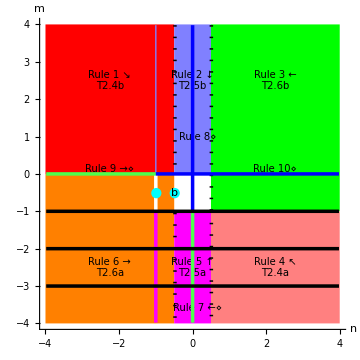

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

## Rules for Specific Points

#### Derivation: Algebraic expansion

#### Rule a: If a^2-b^2≠0, then

∫(A+C Cos[c+d x]^2)/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx  ⟶  C/b∫√Cos[c+d x]ⅆx+1/b∫(A b-a C Cos[c+d x])/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+C_.*Cos[c_.+d_.*x_]^2)/(Sqrt[Cos[c_.+d_.*x_]]*(a_+b_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  Dist[C/b,Int[Sqrt[Cos[c+d*x]],x]] + 
  Dist[1/b,Int[(A*b-a*C*Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*(a+b*Cos[c+d*x])),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

#### Rule b: If a^2-b^2≠0, then

∫(A+C Cos[c+d x]^2)/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx  ⟶  (C √Cos[c+d x] √(a+b Cos[c+d x]) Tan[(c+d x)/2])/(b d)+
C/b∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (1+Cos[c+d x]))ⅆx+1/(2 b)∫(2 A b-a C-a C Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+C_.*Cos[c_.+d_.*x_]^2)/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  C*Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]*Tan[(c+d*x)/2]/(b*d) + 
  Dist[C/b,Int[Sqrt[a+b*Cos[c+d*x]]/(Sqrt[Cos[c+d*x]]*(1+Cos[c+d*x])),x]] + 
  Dist[1/(2*b),Int[(2*A*b-a*C-a*C*Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2]
```

## Rules 7-8: ∫Cos[c+d x]^m(A+C Cos[c+d x]^2)ⅆx

#### Derivation: Recurrence T2.5a with B=0, a=1, b=0, n=0 and A (m+2)+C (m+1)=0

#### Derivation: Recurrence T2.5b with B=0, a=0, b=1, n=0 and A (m+2)+C (m+1)=0

#### Rule 7a: If A(m+2)+C(m+1)=0, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2)ⅆx  ⟶  (C Sin[c+d x]Cos[c+d x]^(m+1))/(d (m+2))

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+C_.*Cos[c_.+d_.*x_]^2),x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+2)) /;
FreeQ[{c,d,A,C,m},x] && ZeroQ[A*(m+2)+C*(m+1)]
```

#### Derivation: Recurrence T2.5a with B=0, a=1, b=0 and n=0

#### Rule 7b: If A(m+2)+C(m+1)≠0 ∧ m<-1, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2)ⅆx  ⟶  
-(A Sin[c+d x]Cos[c+d x]^(m+1))/(d(m+1))+(A(m+2)+C(m+1))/(m+1)∫Cos[c+d x]^(m+2) ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+C_.*Cos[c_.+d_.*x_]^2),x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+1)) + 
  Dist[(A*(m+2)+C*(m+1))/(m+1),Int[Cos[c+d*x]^(m+2),x]] /;
FreeQ[{c,d,A,C},x] && NonzeroQ[A*(m+2)+C*(m+1)] && RationalQ[m] && m<-1
```

#### Derivation: Recurrence T2.5b with B=0, a=0, b=1 and n=0

#### Rule 8: If A(m+2)+C(m+1)≠0 ∧ m≥-1, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2)ⅆx  ⟶  
(C Sin[c+d x]Cos[c+d x]^(m+1))/(d (m+2))+(A(m+2)+C(m+1))/(m+2)∫Cos[c+d x]^m ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+C_.*Cos[c_.+d_.*x_]^2),x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+2)) + 
  Dist[(A*(m+2)+C*(m+1))/(m+2),Int[Cos[c+d*x]^m,x]] /;
FreeQ[{c,d,A,C},x] && NonzeroQ[A*(m+2)+C*(m+1)] && RationalQ[m] && m≥-1
```

## Rules 9-10: ∫(A+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Basis: If a^2 C+b^2 A=0, then A+C z^2=-C/b^2(a-b z) (a+b z)

#### Rule 9a: If a^2 C+b^2 A=0 ∧ n<-1, then

∫(A+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx  ⟶  -C/b^2∫(a-b Cos[c+d x])(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  -Dist[C/b^2,Int[(a-b*Cos[c+d*x])*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && ZeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence T2.6a composed with T2.5b with B=0 and m=0

#### Rule 9b: If a^2-b^2≠0 ∧ a^2 C+b^2 A≠0 ∧ n<-1, then

∫(A+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx  ⟶  
((a^2 C+b^2 A)Sin[c+d x](a+b Cos[c+d x])^(n+1))/(b  d(n+1) (a^2-b^2))+1/(b (n+1) (a^2-b^2))·
∫(a b (A+C)(n+1)-(b^2 A(n+2)+C (a^2+b^2 (n+1))) Cos[c+d x])(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  (a^2*C+b^2*A)*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sim[a*b*(A+C)*(n+1)-(b^2*A*(n+2)+C*(a^2+b^2*(n+1)))*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence T2.5b with B=0 and m=0

#### Rule 10: If n≥-1, then

∫(A+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx  ⟶  
(C Sin[c+d x](a+b Cos[c+d x])^(n+1))/(b d (n+2))+
1/(b (n+2))∫(b(A(n+2)+C(n+1))-a C Cos[c+d x])(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[(A_.+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  C*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[Sim[b*(A*(n+2)+C*(n+1))-a*C*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && RationalQ[n] && n≥-1
```

## Rules 1-6: ∫Cos[c+d x]^m(A+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Derivation: Recurrence T2.4b with B=0 and a^2 C+b^2 A=0

#### Derivation: Recurrence T2.6a with B=0 and a^2 C+b^2 A=0

#### Derivation: Algebraic simplification

#### Basis: If a^2 C+b^2 A=0, then A+C z^2=(C(-a+b z)(a+b z))/b^2

#### Rule 1a: If a^2 C+b^2 A=0 ∧ n<-1/2, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
C/b^2 ∫Cos[c+d x]^m(-a+b Cos[c+d x]) (a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  Dist[C/b^2,Int[Cos[c+d*x]^m*(-a+b*Cos[c+d*x])*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C,m},x] && ZeroQ[a^2*C+b^2*A] && RationalQ[n] && n<-1/2
```

#### Derivation: Recurrence T2.4b with B=0

#### Rule 1b: If a^2-b^2≠0 ∧ a^2 C+b^2 A≠0 ∧ m>0 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
((a^2 C+b^2 A) Sin[c+d x] Cos[c+d x]^m (a+b Cos[c+d x])^(n+1))/(b d (n+1) (a^2-b^2))+1/(b(n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-1)(m (a^2 C+b^2 A)+a b(n+1) (C+A)Cos[c+d x]-(a^2 C(m+1)+b^2 (A (m+n+2)+C (n+1)))Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  (a^2*C+b^2*A)*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-1)*
      Sim[m*(a^2*C+b^2*A)+a*b*(n+1)*(C+A)*Cos[c+d*x]-
        (a^2*C*(m+1)+b^2*(A*(m+n+2)+C*(n+1)))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C+b^2*A] && RationalQ[{m,n}] && 
  m>0 && n<-1/2 && n≠-1
```

#### Derivation: Recurrence T2.5b with B=0

#### Rule 2: If a^2-b^2≠0 ∧ m>0 ∧ (-1/2≤n<1/2 ∨ n=-1), then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
(C Sin[c+d x]Cos[c+d x]^m(a+b Cos[c+d x])^(n+1))/(b d (m+n+2))+1/(b (m+n+2))·
∫Cos[c+d x]^(m-1) (a C m+(b A(m+n+2)+b C(m+n+1))Cos[c+d x]-a C(m+1)Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1)/(b*d*(m+n+2)) + 
  Dist[1/(b*(m+n+2)),
    Int[Cos[c+d*x]^(m-1)*
      Sim[a*C*m+(b*A*(m+n+2)+b*C*(m+n+1))*Cos[c+d*x]-a*C*(m+1)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>0 && (-1/2≤n<1/2 || n==-1)
```

#### Derivation: Recurrence T2.6b with B=0

#### Rule 3: If a^2-b^2≠0 ∧ m≥-1 ∧ n≥1/2, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶                                                         
(C Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^n)/(d (m+n+2))+1/(m+n+2)·
 ∫Cos[c+d x]^m (a (A(m+n+2)+C (m+1))+(b A(m+n+2)+b C(m+n+1))Cos[c+d x]+a C n Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^n/(d*(m+n+2)) + 
  Dist[1/(m+n+2),
    Int[Cos[c+d*x]^m*
      Sim[a*(A*(m+n+2)+C*(m+1))+(b*A*(m+n+2)+b*C*(m+n+1))*Cos[c+d*x]+
        a*C*n*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m≥-1 && n≥1/2
```

#### Derivation: Recurrence T2.4a with B=0

#### Rule 4: If a^2-b^2≠0 ∧ m<-1 ∧ n≥1/2, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(A Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^n)/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(-b A n+(a C(m+1)+a A (m+2)) Cos[c+d x]+b(C(m+1)+A (m+n+2))Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^n/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      Sim[-b*A*n+(a*C*(m+1)+a*A*(m+2))*Cos[c+d*x]+b*(C*(m+1)+A*(m+n+2))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && n≥1/2
```

#### Derivation: Recurrence T2.5a with B=0

#### Rule 5: If a^2-b^2≠0 ∧ m<-1 ∧ (-1/2≤n<1/2 ∨ n=-1), then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(A Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d(m+1))+1/(a (m+1))·
∫Cos[c+d x]^(m+1) (-b A (m+n+2)+a(A(m+2)+C(m+1))Cos[c+d x]+b A(m+n+3)Cos[c+d x]^2 )(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(m+1)) + 
  Dist[1/(a*(m+1)),
    Int[Cos[c+d*x]^(m+1)*
      Sim[-b*A*(m+n+2)+a*(A*(m+2)+C*(m+1))*Cos[c+d*x]+b*A*(m+n+3)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && (-1/2≤n<1/2 || n==-1)
```

#### Derivation: Recurrence T2.6a with B=0

#### Rule 6: If a^2-b^2≠0 ∧ a^2 C+b^2 A≠0 ∧ m<0 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
-((a^2 C+b^2 A) Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
 ∫Cos[c+d x]^m (A (a^2 (n+1)-b^2 (m+n+2))-a^2 C (m+1)-a(n+1)(b A+b C)Cos[c+d x]+(m+n+3) (a^2 C+b^2 A)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -(a^2*C+b^2*A)*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^m*
      Sim[A*(a^2*(n+1)-b^2*(m+n+2))-a^2*C*(m+1)-a*(n+1)*(b*A+b*C)*Cos[c+d*x]+
        (m+n+3)*(a^2*C+b^2*A)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C+b^2*A] && RationalQ[{m,n}] && 
  m<0 && n<-1/2 && n≠-1
```

# Integration Rules for ∫cos^m(z)(A+B cos(z)+C cos^2(z))(a+b cos(z))^n ⅆz when a^2≠b^2

## Domain Map of Rules

-Graphics-

Legend:
•  The rule number in a colored region indicates the rule to use for integrals in that region.
•  The rule number next to a colored line indicates the rule to use for integrals on that line.
•  A white region or line indicates there is no rule for integrals in that region or on that line.
•  A solid black line indicates integrals on that line are handled by rules in another section.
•  A dashed black line on the border of a region indicates integrals on that border are handled by the rule for that region.
•  The arrow(s) following a rule number indicates the direction the rule drives integrands in the n×m exponent plane.
•  A ⋄ following a rule number indicates the rule transforms the integrand into a form handled by another section.
•  A red (stop) disk indicates the terminal rule to use for the point at the center of the disk.
•  A cyan disk indicates the non-terminal rule to use for the point at the center of the disk.

## Rules for Specific Points

#### Derivation: Algebraic expansion

#### Rule a: If a^2-b^2≠0, then

∫(A+B Cos[c+d x]+C Cos[c+d x]^2)/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx  ⟶  C/b∫√Cos[c+d x]ⅆx+1/b∫(A b+(b B-a C) Cos[c+d x])/(√Cos[c+d x] (a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)/(Sqrt[Cos[c_.+d_.*x_]]*(a_+b_.*Cos[c_.+d_.*x_])),x_Symbol] :=
  Dist[C/b,Int[Sqrt[Cos[c+d*x]],x]] + 
  Dist[1/b,Int[(A*b+(b*B-a*C)*Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*(a+b*Cos[c+d*x])),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

#### Rule b: If a^2-b^2≠0, then

∫(A+B Cos[c+d x]+C Cos[c+d x]^2)/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx  ⟶  (C √Cos[c+d x] √(a+b Cos[c+d x]) Tan[(c+d x)/2])/(b d)+
C/b∫(√(a+b Cos[c+d x]))/(√Cos[c+d x] (1+Cos[c+d x]))ⅆx+1/(2 b)∫(2 A b-a C+(2 b B-a C) Cos[c+d x])/(√Cos[c+d x] √(a+b Cos[c+d x]))ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)/(Sqrt[Cos[c_.+d_.*x_]]*Sqrt[a_+b_.*Cos[c_.+d_.*x_]]),x_Symbol] :=
  C*Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]*Tan[(c+d*x)/2]/(b*d) + 
  Dist[C/b,Int[Sqrt[a+b*Cos[c+d*x]]/(Sqrt[Cos[c+d*x]]*(1+Cos[c+d*x])),x]] + 
  Dist[1/(2*b),Int[(2*A*b-a*C+(2*b*B-a*C)*Cos[c+d*x])/(Sqrt[Cos[c+d*x]]*Sqrt[a+b*Cos[c+d*x]]),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2]
```

## Rules 7-8: ∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2)ⅆx

#### Derivation: Algebraic simplification

#### Rule 7a: If m≤-1, then

∫Cos[c+d x]^m(B Cos[c+d x]+C Cos[c+d x]^2)ⅆx  ⟶  ∫Cos[c+d x]^(m+1) (B+C Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2),x_Symbol] :=
  Int[Cos[c+d*x]^(m+1)*(B+C*Cos[c+d*x]),x] /;
FreeQ[{c,d,B,C},x] && RationalQ[m] && m≤-1
```

#### Derivation: Recurrence T2.5a with a=1, b=0 and n=0

#### Rule 7b: If m<-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2)ⅆx  ⟶  
-(A Sin[c+d x]Cos[c+d x]^(m+1))/(d(m+1))+1/(m+1)∫Cos[c+d x]^(m+1) (B(m+1)+(A(m+2)+C(m+1))Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2),x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+1)) + 
  Dist[1/(m+1),Int[Cos[c+d*x]^(m+1)*Sim[B*(m+1)+(A*(m+2)+C*(m+1))*Cos[c+d*x],x],x]] /;
FreeQ[{c,d,A,B,C},x] && RationalQ[m] && m<-1
```

#### Derivation: Recurrence T2.5b with a=0, b=1 and n=0

#### Rule 8: If m≥-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2)ⅆx  ⟶  
(C Sin[c+d x]Cos[c+d x]^(m+1))/(d (m+2))+1/(m+2)∫Cos[c+d x]^m (A(m+2)+C(m+1)+B(m+2)Cos[c+d x])ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2),x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^(m+1)/(d*(m+2)) + 
  Dist[1/(m+2),Int[Cos[c+d*x]^m*Sim[A*(m+2)+C*(m+1)+B*(m+2)*Cos[c+d*x],x],x]] /;
FreeQ[{c,d,A,B,C},x] && RationalQ[m] && m≥-1
```

## Rules 9-10: ∫(A+B Cos[c+d x]+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Derivation: Algebraic simplification

#### Basis: If a^2 C-a b B+b^2 A=0, then A+B z+C z^2=1/b^2(b B-a C+b C z)(a+b z)

#### Rule 9a: If a^2 C-a b B+b^2 A=0 ∧ n<-1, then

∫(A+B Cos[c+d x]+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx  ⟶  
1/b^2∫(b B-a C+b C Cos[c+d x])(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  Dist[1/b^2,Int[Sim[b*B-a*C+b*C*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && ZeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence T2.4b with m=0

#### Rule 9b: If a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ n<-1, then

∫(A+B Cos[c+d x]+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx  ⟶  
((a^2 C-a b B+b^2 A)Sin[c+d x](a+b Cos[c+d x])^(n+1))/(b  d(n+1) (a^2-b^2))+1/(b (n+1) (a^2-b^2))·
∫(b (a (A+C)-b B) (n+1)-(b (b A-a B) (n+2)+C (a^2+b^2 (n+1))) Cos[c+d x])(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  (a^2*C-a*b*B+b^2*A)*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Sim[b*(a*(A+C)-b*B)*(n+1)-(b*(b*A-a*B)*(n+2)+C*(a^2+b^2*(n+1)))*Cos[c+d*x],x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1
```

#### Derivation: Recurrence T2.5b with m=0

#### Rule 10: If n≥-1, then

∫(A+B Cos[c+d x]+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx  ⟶  
(C Sin[c+d x](a+b Cos[c+d x])^(n+1))/(b d (n+2))+
1/(b (n+2))∫(b(A(n+2)+C(n+1))+(b B(n+2)-a C)Cos[c+d x])(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  C*Sin[c+d*x]*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+2)) + 
  Dist[1/(b*(n+2)),
    Int[Sim[b*(A*(n+2)+C*(n+1))+(b*B*(n+2)-a*C)*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && RationalQ[n] && n≥-1
```

## Rules 1-6: ∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Derivation: Recurrence T2.4b with a^2 C-a b B+b^2 A=0

#### Derivation: Recurrence T2.6a with a^2 C-a b B+b^2 A=0

#### Derivation: Algebraic simplification

#### Basis: If a^2 C-a b B+b^2 A=0, then A+B z+C z^2=((b B-a C+b C z)(a+b z))/b^2

#### Rule 1a: If a^2 C-a b B+b^2 A=0 ∧ n<-1/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
1/b^2 ∫Cos[c+d x]^m(b B-a C+b C Cos[c+d x]) (a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  Dist[1/b^2,Int[Cos[c+d*x]^m*Sim[b*B-a*C+b*C*Cos[c+d*x],x]*(a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C,m},x] && ZeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[n] && n<-1/2
```

#### Derivation: Recurrence T2.4b

#### Rule 1b: If a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ m>0 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
((a^2 C-a b B+b^2 A) Sin[c+d x] Cos[c+d x]^m (a+b Cos[c+d x])^(n+1))/(b d (n+1) (a^2-b^2))+1/(b(n+1)(a^2-b^2))·
∫Cos[c+d x]^(m-1)(m (a^2 C-a b B+b^2 A)+b(n+1)(a (C+A)-b B)Cos[c+d x]-(a^2 C(m+1)-a b B (m+n+2)+b^2 (A (m+n+2)+C (n+1)))Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  (a^2*C-a*b*B+b^2*A)*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1)/(b*d*(n+1)*(a^2-b^2))+
  Dist[1/(b*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^(m-1)*
      Sim[m*(a^2*C-a*b*B+b^2*A)+b*(n+1)*(a*(C+A)-b*B)*Cos[c+d*x]-
        (a^2*C*(m+1)-a*b*B*(m+n+2)+b^2*(A*(m+n+2)+C*(n+1)))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[{m,n}] && 
  m>0 && n<-1/2 && n≠-1
```

#### Derivation: Recurrence T2.5b

#### Rule 2: If a^2-b^2≠0 ∧ m>0 ∧ (-1/2≤n<1/2 ∨ n=-1), then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
(C Sin[c+d x]Cos[c+d x]^m(a+b Cos[c+d x])^(n+1))/(b d (m+n+2))+1/(b (m+n+2))·
∫Cos[c+d x]^(m-1) (a C m+b(A(m+n+2)+C(m+n+1))Cos[c+d x]+(b B(m+n+2)-a C(m+1))Cos[c+d x]^2)(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^m*(a+b*Cos[c+d*x])^(n+1)/(b*d*(m+n+2)) + 
  Dist[1/(b*(m+n+2)),
    Int[Cos[c+d*x]^(m-1)*
      Sim[a*C*m+b*(A*(m+n+2)+C*(m+n+1))*Cos[c+d*x]+(b*B*(m+n+2)-a*C*(m+1))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m>0 && (-1/2≤n<1/2 || n==-1)
```

#### Derivation: Recurrence T2.6b

#### Rule 3: If a^2-b^2≠0 ∧ m≥-1 ∧ n≥1/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
(C Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^n)/(d (m+n+2))+1/(m+n+2)·
 ∫Cos[c+d x]^m (a (A(m+n+2)+C (m+1))+((b A+a B)(m+n+2)+b C(m+n+1))Cos[c+d x]+(b B (m+n+2)+a C n)Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_.*(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  C*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^n/(d*(m+n+2)) + 
  Dist[1/(m+n+2),
    Int[Cos[c+d*x]^m*
      Sim[a*(A*(m+n+2)+C*(m+1))+((b*A+a*B)*(m+n+2)+b*C*(m+n+1))*Cos[c+d*x]+
        (b*B*(m+n+2)+a*C*n)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m≥-1 && n≥1/2
```

#### Derivation: Recurrence T2.4a

#### Rule 4: If a^2-b^2≠0 ∧ m<-1 ∧ n≥1/2, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(A Sin[c+d x] Cos[c+d x]^(m+1) (a+b Cos[c+d x])^n)/(d(m+1))+1/(m+1)·
∫Cos[c+d x]^(m+1)(a B(m+1)-b A n+((a C+b B) (m+1)+a A (m+2)) Cos[c+d x]+b(C(m+1)+A (m+n+2))Cos[c+d x]^2)(a+b Cos[c+d x])^(n-1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_.,x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^n/(d*(m+1)) + 
  Dist[1/(m+1),
    Int[Cos[c+d*x]^(m+1)*
      Sim[a*B*(m+1)-b*A*n+((a*C+b*B)*(m+1)+a*A*(m+2))*Cos[c+d*x]+b*(C*(m+1)+A*(m+n+2))*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n-1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && n≥1/2
```

#### Derivation: Recurrence T2.5a

#### Rule 5: If a^2-b^2≠0 ∧ m<-1 ∧ (-1/2≤n<1/2 ∨ n=-1), then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
-(A Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d(m+1))+1/(a (m+1))·
∫Cos[c+d x]^(m+1) (a B(m+1)-b A (m+n+2)+a(A(m+2)+C(m+1))Cos[c+d x]+b A(m+n+3)Cos[c+d x]^2 )(a+b Cos[c+d x])^n ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -A*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(m+1)) + 
  Dist[1/(a*(m+1)),
    Int[Cos[c+d*x]^(m+1)*
       Sim[a*B*(m+1)-b*A*(m+n+2)+a*(A*(m+2)+C*(m+1))*Cos[c+d*x]+b*A*(m+n+3)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^n,x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && RationalQ[{m,n}] && m<-1 && (-1/2≤n<1/2 || n==-1)
```

#### Derivation: Recurrence T2.6a

#### Rule 6: If a^2-b^2≠0 ∧ a^2 C-a b B+b^2 A≠0 ∧ m<0 ∧ n<-1/2 ∧ n≠-1, then

∫Cos[c+d x]^m(A+B Cos[c+d x]+C Cos[c+d x]^2) (a+b Cos[c+d x])^n ⅆx  ⟶  
-((a^2 C-a b B+b^2 A) Sin[c+d x]Cos[c+d x]^(m+1)(a+b Cos[c+d x])^(n+1))/(a d (n+1) (a^2-b^2))+1/(a (n+1) (a^2-b^2))·
 ∫Cos[c+d x]^m (A (a^2 (n+1)-b^2 (m+n+2))-a (a C-b B) (m+1)-a(n+1)(b A-a B+b C)Cos[c+d x]+(m+n+3) (a^2 C-a b B+b^2 A)Cos[c+d x]^2)(a+b Cos[c+d x])^(n+1)ⅆx

#### Program code:

```mathematica
Int[Cos[c_.+d_.*x_]^m_*(A_.+B_.*Cos[c_.+d_.*x_]+C_.*Cos[c_.+d_.*x_]^2)*(a_+b_.*Cos[c_.+d_.*x_])^n_,x_Symbol] :=
  -(a^2*C-a*b*B+b^2*A)*Sin[c+d*x]*Cos[c+d*x]^(m+1)*(a+b*Cos[c+d*x])^(n+1)/(a*d*(n+1)*(a^2-b^2)) + 
  Dist[1/(a*(n+1)*(a^2-b^2)),
    Int[Cos[c+d*x]^m*
      Sim[A*(a^2*(n+1)-b^2*(m+n+2))-a*(a*C-b*B)*(m+1)-a*(n+1)*(b*A-a*B+b*C)*Cos[c+d*x]+
        (m+n+3)*(a^2*C-a*b*B+b^2*A)*Cos[c+d*x]^2,x]*
      (a+b*Cos[c+d*x])^(n+1),x]] /;
FreeQ[{a,b,c,d,A,B,C},x] && NonzeroQ[a^2-b^2] && NonzeroQ[a^2*C-a*b*B+b^2*A] && RationalQ[{m,n}] && 
  m<0 && n<-1/2 && n≠-1
```